```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 200 Kb

{Utilities`CleanSlate`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,System`,Global`}

```mathematica
Clear[rBC]
rBC = { x[t] + 1/2 a Sin[θ1[t]] , y[t] + 1/2 a Cos[θ1[t]] }
```

{1/2 a Sin[θ1[t]]+x[t],1/2 a Cos[θ1[t]]+y[t]}

```mathematica
D[rBC, t]
```

{x'[t]+1/2 a Cos[θ1[t]] θ1'[t],y'[t]-1/2 a Sin[θ1[t]] θ1'[t]}

```mathematica
D[rBC, t] . D[rBC, t]
```

(x'[t]+1/2 a Cos[θ1[t]] θ1'[t])^2+(y'[t]-1/2 a Sin[θ1[t]] θ1'[t])^2

```mathematica
D[rBC, t] . D[rBC, t]  // Expand
```

x'[t]^2+y'[t]^2+a Cos[θ1[t]] x'[t] θ1'[t]-a Sin[θ1[t]] y'[t] θ1'[t]+1/4 a^2 Cos[θ1[t]]^2 θ1'[t]^2+1/4 a^2 Sin[θ1[t]]^2 θ1'[t]^2

```mathematica
D[rBC, t] . D[rBC, t]  // Expand  // Simplify
```

x'[t]^2+y'[t]^2+a Cos[θ1[t]] x'[t] θ1'[t]-a Sin[θ1[t]] y'[t] θ1'[t]+1/4 a^2 θ1'[t]^2

```mathematica
Clear[rAB]
rAB =  { x[t] + 1/2 a Sin[θ2[t]] , y[t] + 1/2 a Cos[θ2[t]] }
```

{1/2 a Sin[θ2[t]]+x[t],1/2 a Cos[θ2[t]]+y[t]}

```mathematica
D[rAB, t]
```

{x'[t]+1/2 a Cos[θ2[t]] θ2'[t],y'[t]-1/2 a Sin[θ2[t]] θ2'[t]}

```mathematica
D[rAB, t] . D[rAB, t]
```

(x'[t]+1/2 a Cos[θ2[t]] θ2'[t])^2+(y'[t]-1/2 a Sin[θ2[t]] θ2'[t])^2

```mathematica
D[rAB, t] . D[rAB, t]  // Expand
```

x'[t]^2+y'[t]^2+a Cos[θ2[t]] x'[t] θ2'[t]-a Sin[θ2[t]] y'[t] θ2'[t]+1/4 a^2 Cos[θ2[t]]^2 θ2'[t]^2+1/4 a^2 Sin[θ2[t]]^2 θ2'[t]^2

```mathematica
D[rAB, t] . D[rAB, t]  // Expand // Simplify
```

x'[t]^2+y'[t]^2+a Cos[θ2[t]] x'[t] θ2'[t]-a Sin[θ2[t]] y'[t] θ2'[t]+1/4 a^2 θ2'[t]^2

```mathematica
Clear[T]
T = 1/2 m ( D[rBC, t] . D[rBC, t]    )  + 1/2(1/12 m a^2 θ1'[t]^2) +
1/2 m ( D[rAB, t] . D[rAB, t]    ) +  1/2(1/12 m a^2 θ2'[t]^2)  // Expand // Simplify
```

1/6 m (6 x'[t]^2+6 y'[t]^2+3 a x'[t] (Cos[θ1[t]] θ1'[t]+Cos[θ2[t]] θ2'[t])-3 a y'[t] (Sin[θ1[t]] θ1'[t]+Sin[θ2[t]] θ2'[t])+a^2 (θ1'[t]^2+θ2'[t]^2))

```mathematica
T // pdConv
```

1/6 m (a^2 (((∂θ1(t))/(∂t))^2+((∂θ2(t))/(∂t))^2)+3 a (∂x(t))/(∂t) ((∂θ1(t))/(∂t) cos(θ1(t))+(∂θ2(t))/(∂t) cos(θ2(t)))-3 a (∂y(t))/(∂t) ((∂θ1(t))/(∂t) sin(θ1(t))+(∂θ2(t))/(∂t) sin(θ2(t)))+6 ((∂x(t))/(∂t))^2+6 ((∂y(t))/(∂t))^2)

```mathematica
Clear[V]
V = 0
```

0

```mathematica
Clear[ℒ]
ℒ = T - V
```

1/6 m (6 x'[t]^2+6 y'[t]^2+3 a x'[t] (Cos[θ1[t]] θ1'[t]+Cos[θ2[t]] θ2'[t])-3 a y'[t] (Sin[θ1[t]] θ1'[t]+Sin[θ2[t]] θ2'[t])+a^2 (θ1'[t]^2+θ2'[t]^2))

```mathematica
Clear[q]
q = {x[t], y[t] , θ1[t] , θ2[t] }
```

{x[t],y[t],θ1[t],θ2[t]}

```mathematica
D[ D[ ℒ , D[q[[1]], t] ] , t] - D[ ℒ , q[[1]] ] == 0 // Expand // Simplify 
D[ D[ ℒ , D[q[[2]], t] ] , t] - D[ ℒ , q[[2]] ] == 0 // Expand // Simplify 
D[ D[ ℒ , D[q[[3]], t] ] , t] - D[ ℒ , q[[3]] ] == 0 // Expand // Simplify 
D[ D[ ℒ , D[q[[4]], t] ] , t] - D[ ℒ , q[[4]] ] == 0 // Expand // Simplify
```

a m (Sin[θ1[t]] θ1'[t]^2+Sin[θ2[t]] θ2'[t]^2)==m (4 x''[t]+a Cos[θ1[t]] θ1''[t]+a Cos[θ2[t]] θ2''[t])

m (a Cos[θ1[t]] θ1'[t]^2+a Cos[θ2[t]] θ2'[t]^2-4 y''[t]+a Sin[θ1[t]] θ1''[t]+a Sin[θ2[t]] θ2''[t])==0

a m (3 Cos[θ1[t]] x''[t]-3 Sin[θ1[t]] y''[t]+2 a θ1''[t])==0

a m (3 Cos[θ2[t]] x''[t]-3 Sin[θ2[t]] y''[t]+2 a θ2''[t])==0

```mathematica
Table[
D[ D[ ℒ , D[q[[i]], t] ] , t] - D[ ℒ , q[[i]] ] == 0 // Expand // Simplify ,
{ i, 1, 4 } ] // TableForm
```

a m (Sin[θ1[t]] θ1'[t]^2+Sin[θ2[t]] θ2'[t]^2)==m (4 x''[t]+a Cos[θ1[t]] θ1''[t]+a Cos[θ2[t]] θ2''[t])
m (a Cos[θ1[t]] θ1'[t]^2+a Cos[θ2[t]] θ2'[t]^2-4 y''[t]+a Sin[θ1[t]] θ1''[t]+a Sin[θ2[t]] θ2''[t])==0
a m (3 Cos[θ1[t]] x''[t]-3 Sin[θ1[t]] y''[t]+2 a θ1''[t])==0
a m (3 Cos[θ2[t]] x''[t]-3 Sin[θ2[t]] y''[t]+2 a θ2''[t])==0

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q , t ] ;
eqs // TableForm
```

1/2 m (a Sin[θ1[t]] θ1'[t]^2+a Sin[θ2[t]] θ2'[t]^2-4 x''[t]-a Cos[θ1[t]] θ1''[t]-a Cos[θ2[t]] θ2''[t])==0
1/2 m (a Cos[θ1[t]] θ1'[t]^2+a Cos[θ2[t]] θ2'[t]^2-4 y''[t]+a Sin[θ1[t]] θ1''[t]+a Sin[θ2[t]] θ2''[t])==0
-1/6 a m (3 Cos[θ1[t]] x''[t]-3 Sin[θ1[t]] y''[t]+2 a θ1''[t])==0
-1/6 a m (3 Cos[θ2[t]] x''[t]-3 Sin[θ2[t]] y''[t]+2 a θ2''[t])==0

```mathematica
Clear[parameters]
parameters = { 
a -> 2 ,
m -> 10 
} ;
parameters // TableForm
```

a→2
m→10

```mathematica
eqs /. parameters  // TableForm
```

5 (2 Sin[θ1[t]] θ1'[t]^2+2 Sin[θ2[t]] θ2'[t]^2-4 x''[t]-2 Cos[θ1[t]] θ1''[t]-2 Cos[θ2[t]] θ2''[t])==0
5 (2 Cos[θ1[t]] θ1'[t]^2+2 Cos[θ2[t]] θ2'[t]^2-4 y''[t]+2 Sin[θ1[t]] θ1''[t]+2 Sin[θ2[t]] θ2''[t])==0
-10/3 (3 Cos[θ1[t]] x''[t]-3 Sin[θ1[t]] y''[t]+4 θ1''[t])==0
-10/3 (3 Cos[θ2[t]] x''[t]-3 Sin[θ2[t]] y''[t]+4 θ2''[t])==0

```mathematica
Clear[ics] 
ics = { 
θ1[0] == - π / 2 ,
θ2[0] == π / 2 , 
x[0] == 0 ,
y[0] == 0 ,
θ1'[0] ==  0 ,
θ2'[0] ==   2,
x'[0] ==   0 ,
y'[0] ==  0 
} ;
ics // TableForm
```

θ1[0]==-π/2
θ2[0]==π/2
x[0]==0
y[0]==0
θ1'[0]==0
θ2'[0]==2
x'[0]==0
y'[0]==0

```mathematica
Clear[solution]
solution[t_] = 
First[NDSolve[ Union[ eqs /. parameters , ics ] , q, { t, 0, 200 } ] ]
```

{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t],θ1[t]→InterpolatingFunction[…][t],θ2[t]→InterpolatingFunction[…][t]}

```mathematica
Plot[ Evaluate[ q /. solution[t] ] , { t, 0, 10 } , PlotLabels -> q ]
```

-Graphics-

```mathematica
solution[t]
solution[t][[1]]
solution[t][[1,2]]
```

{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t],θ1[t]→InterpolatingFunction[…][t],θ2[t]→InterpolatingFunction[…][t]}

x[t]→InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

```mathematica
Animate[
ParametricPlot[  { solution[t][[1,2]] , solution'[t][[1,2]] } , { t , 0, tmax } , 
AxesLabel-> { q[[1]] , D[q[[1]], t] }  ]  , { tmax , 0.1 , 100 } ]
```

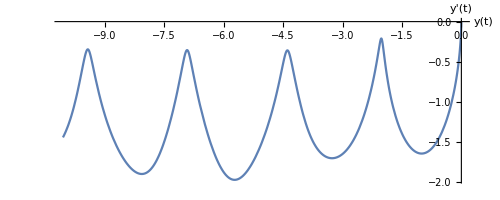

```mathematica
ParametricPlot[  { solution[t][[2,2]] , solution'[t][[2,2]] } , { t , 0, 10 } , 
AxesLabel-> { q[[2]] , D[q[[2]], t] }  ]
```

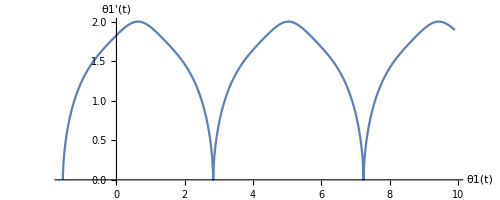

```mathematica
ParametricPlot[  { solution[t][[3,2]] , solution'[t][[3,2]] } , { t , 0, 10 } , 
AxesLabel-> { q[[3]] , D[q[[3]], t] }  ]
```

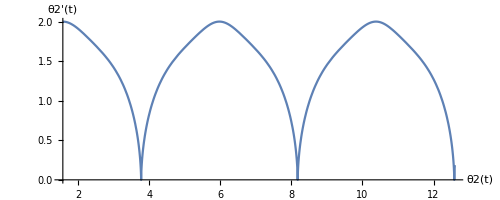

```mathematica
ParametricPlot[  { solution[t][[4,2]] , solution'[t][[4,2]] } , { t , 0, 10 } , 
AxesLabel-> { q[[4]] , D[q[[4]], t] }  ]
```

```mathematica
D[q, t]
```

{x'[t],y'[t],θ1'[t],θ2'[t]}

```mathematica
D[ T , D[q[[1]], t] ] // Expand
```

2 m x'[t]+1/2 a m Cos[θ1[t]] θ1'[t]+1/2 a m Cos[θ2[t]] θ2'[t]

```mathematica
D[ T , D[q[[2]], t] ]  // Expand
```

2 m y'[t]-1/2 a m Sin[θ1[t]] θ1'[t]-1/2 a m Sin[θ2[t]] θ2'[t]

```mathematica
D[ T , D[q[[3]], t] ] // Expand
```

1/2 a m Cos[θ1[t]] x'[t]-1/2 a m Sin[θ1[t]] y'[t]+1/3 a^2 m θ1'[t]

```mathematica
D[ T , D[q[[4]], t] ] // Expand
```

1/2 a m Cos[θ2[t]] x'[t]-1/2 a m Sin[θ2[t]] y'[t]+1/3 a^2 m θ2'[t]

```mathematica
Table[
D[ T , D[q[[i]], t] ] // Expand  ,
{ i, 1, 4 } ] // TableForm
```

2 m x'[t]+1/2 a m Cos[θ1[t]] θ1'[t]+1/2 a m Cos[θ2[t]] θ2'[t]
2 m y'[t]-1/2 a m Sin[θ1[t]] θ1'[t]-1/2 a m Sin[θ2[t]] θ2'[t]
1/2 a m Cos[θ1[t]] x'[t]-1/2 a m Sin[θ1[t]] y'[t]+1/3 a^2 m θ1'[t]
1/2 a m Cos[θ2[t]] x'[t]-1/2 a m Sin[θ2[t]] y'[t]+1/3 a^2 m θ2'[t]